# PHY410: Homework 1, Problem 2

## part (a) (tests)

```mathematica
Random[]
```

0.429285

```mathematica
Random[Integer]
```

0

```mathematica
Table[Random[Integer], {10}]
```

{1,0,0,0,1,0,0,0,1,1}

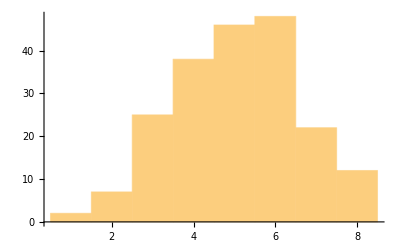

```mathematica
NumberOfHeads[n_] := Sum[Random[Integer], {n}]
ManyTrials[N_] := Table[NumberOfHeads[10], {N}]
Histogram[ManyTrials[200]]
```

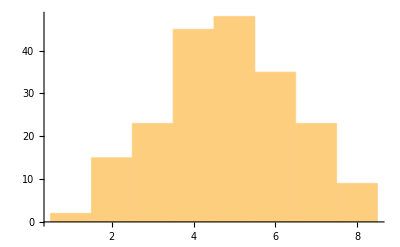

```mathematica
Histogram[Table[Sum[Random[Integer], {10}], {200}]]
```

## part (b)

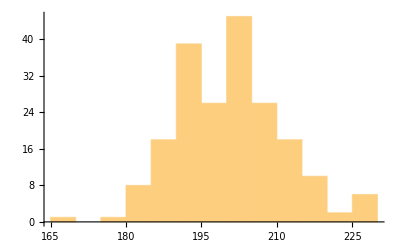

```mathematica
Histogram[Table[Sum[Random[Integer], {400}], {200}]]
```

Mathematica chose a bin width of 5, but I want the bni width to be 1, otherwise the Gaussian fit in part (d) won’t work. So I asked for 60 bins...

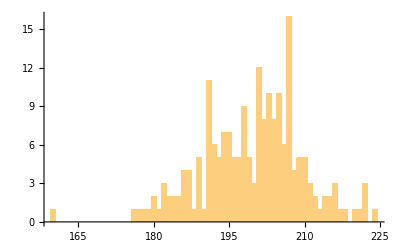

```mathematica
Histogram[Table[Sum[Random[Integer], {400}], {200}], 60]
```

## part (c)

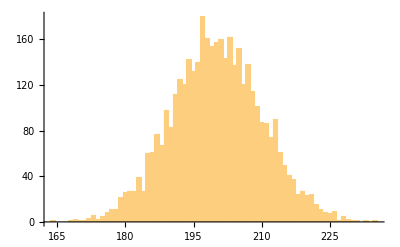

```mathematica
P1 = Histogram[Table[Sum[Random[Integer], {400}], {4000}], 80]
```

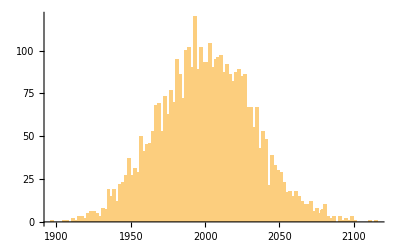

```mathematica
P3 = Histogram[Table[Sum[Random[Integer], {4000}], {4000}], 80]
```

## part (d)

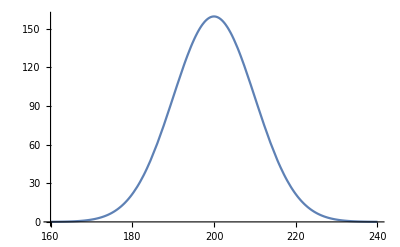

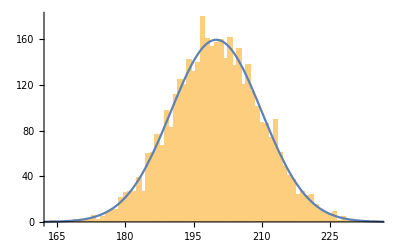

```mathematica
P2 = Plot[4000*Sqrt[2/(400*Pi)]*Exp[-2*(x-200)^2/400], {x, 160, 240}]
Show[P1, P2]
```